```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ken_l/Documents/active-ads/images

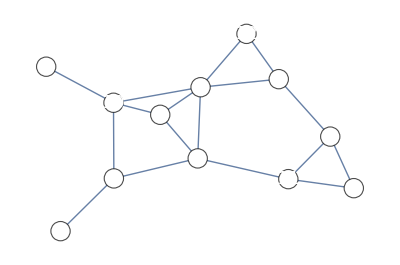

fig-compute-distance-graph.png

(0 | 2 | 2 | 2 | 3 | 1 | 1 | 3 | 3 | 1 | 2 | 2
2 | 0 | 3 | 3 | 2 | 2 | 1 | 4 | 1 | 2 | 2 | 1
2 | 3 | 0 | 2 | 5 | 3 | 2 | 3 | 4 | 1 | 4 | 3
2 | 3 | 2 | 0 | 3 | 1 | 2 | 1 | 3 | 1 | 2 | 3
3 | 2 | 5 | 3 | 0 | 2 | 3 | 4 | 1 | 4 | 1 | 3
1 | 2 | 3 | 1 | 2 | 0 | 1 | 2 | 2 | 2 | 1 | 2
1 | 1 | 2 | 2 | 3 | 1 | 0 | 3 | 2 | 1 | 2 | 1
3 | 4 | 3 | 1 | 4 | 2 | 3 | 0 | 4 | 2 | 3 | 4
3 | 1 | 4 | 3 | 1 | 2 | 2 | 4 | 0 | 3 | 1 | 2
1 | 2 | 1 | 1 | 4 | 2 | 1 | 2 | 3 | 0 | 3 | 2
2 | 2 | 4 | 2 | 1 | 1 | 2 | 3 | 1 | 3 | 0 | 3
2 | 1 | 3 | 3 | 3 | 2 | 1 | 4 | 2 | 2 | 3 | 0)

```mathematica
SeedRandom[69];
n = 12; e = 17;
(DG=RandomGraph[{n, e}, EdgeLabels -> None, EdgeLabelStyle -> Larger, VertexLabelStyle -> Directive[Italic, 18], VertexSize -> Large, VertexStyle -> White, VertexLabels -> Table[i -> Placed[ToString[i], Center], {i, 1, n}]])
DG//Export["fig-compute-distance-graph.png",#,"PNG"]&
Dee=GraphDistanceMatrix[DG]
```

```mathematica
{BreadthFirstScan[DG,2]}//Prepend[#,Range[12]]&//Transpose//Prepend[#,{"vertex","vertex.from"}]&//Transpose//TableForm//TeXForm
```

\begin{array}{ccccccccccccc}
 \text{vertex} & 1 & 2 & 3 & 4 & 5 & 6
   & 7 & 8 & 9 & 10 & 11 & 12 \\
 \text{vertex.from} & 7 & 2 & 10 & 6 &
   9 & 7 & 2 & 4 & 2 & 7 & 9 & 2 \\
\end{array}

```mathematica
{BreadthFirstScan[DG,2]}//Prepend[#,Range[12]]&//Transpose//Prepend[#,{"vertex","vertex.from"}]&//Transpose//TableForm
```

vertex | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
vertex.from | 7 | 2 | 10 | 6 | 9 | 7 | 2 | 4 | 2 | 7 | 9 | 2

```mathematica
Dee//TeXForm
```

\left(
\begin{array}{cccccccccccc}
 0 & 2 & 2 & 2 & 3 & 1 & 1 & 3 & 3 & 1
   & 2 & 2 \\
 2 & 0 & 3 & 3 & 2 & 2 & 1 & 4 & 1 & 2
   & 2 & 1 \\
 2 & 3 & 0 & 2 & 5 & 3 & 2 & 3 & 4 & 1
   & 4 & 3 \\
 2 & 3 & 2 & 0 & 3 & 1 & 2 & 1 & 3 & 1
   & 2 & 3 \\
 3 & 2 & 5 & 3 & 0 & 2 & 3 & 4 & 1 & 4
   & 1 & 3 \\
 1 & 2 & 3 & 1 & 2 & 0 & 1 & 2 & 2 & 2
   & 1 & 2 \\
 1 & 1 & 2 & 2 & 3 & 1 & 0 & 3 & 2 & 1
   & 2 & 1 \\
 3 & 4 & 3 & 1 & 4 & 2 & 3 & 0 & 4 & 2
   & 3 & 4 \\
 3 & 1 & 4 & 3 & 1 & 2 & 2 & 4 & 0 & 3
   & 1 & 2 \\
 1 & 2 & 1 & 1 & 4 & 2 & 1 & 2 & 3 & 0
   & 3 & 2 \\
 2 & 2 & 4 & 2 & 1 & 1 & 2 & 3 & 1 & 3
   & 0 & 3 \\
 2 & 1 & 3 & 3 & 3 & 2 & 1 & 4 & 2 & 2
   & 3 & 0 \\
\end{array}
\right)

```mathematica
Max[Dee]
```

5

```mathematica
Map[Max,Dee]
```

{3,4,5,3,5,3,3,4,4,4,4,4}

```mathematica
{1,4,6,7}
```

```mathematica
DG
```

-Graphics-

```mathematica
A= Normal[AdjacencyMatrix[DG]];Map[{#,Flatten[Position[A[[#]],1]]}&, Range[12]]//StandardForm//Print
```

{{1,{6,7,10}},{2,{7,9,12}},{3,{10}},{4,{6,8,10}},{5,{9,11}},{6,{1,4,7,11}},{7,{1,2,6,10,12}},{8,{4}},{9,{2,5,11}},{10,{1,3,4,7}},{11,{5,6,9}},{12,{2,7}}}